```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
realData = Import["tennis.csv", "CSV"];
eulerData = Import["euler_solver.csv", "CSV"];
rk4Data = Import["rk4_solver.csv", "CSV"];
adaptData = Import["adapt_solver.csv", "CSV"];
pinnData = Import["pinn_data.csv", "CSV"];
```

```mathematica
realDataTY = Table[{realData[[i]][[1]]-realData[[2]][[1]],-realData[[i]][[2]]-realData[[2]][[2]]},{i,2,Length[realData]}];
```

```mathematica
(*t = Table[pinnData[[i]][[1]],{i,2,Length[pinnData]}];
y = Table[pinnData[[i]][[2]],{i,2,Length[pinnData]}];*)
eulerData = Table[{eulerData[[i]][[1]],eulerData[[i]][[2]]},{i,2,Length[eulerData]}];
rk4Data = Table[{rk4Data[[i]][[1]],rk4Data[[i]][[2]]},{i,2,Length[rk4Data]}];
adaptData =  Table[{adaptData[[i]][[1]],adaptData[[i]][[2]]},{i,2,Length[adaptData]}];
pinnDataTY = Table[{pinnData[[i]][[1]],-pinnData[[i]][[2]]},{i,2,Length[pinnData]}];
```

```mathematica
dataInterpolated = Interpolation[realDataTY];
eulerInterpolated = Interpolation[eulerData];
rk4Interpolated = Interpolation[rk4Data];
adaptInterpolated = Interpolation[adaptData];
pinnInterpolated = Interpolation[pinnDataTY];
```

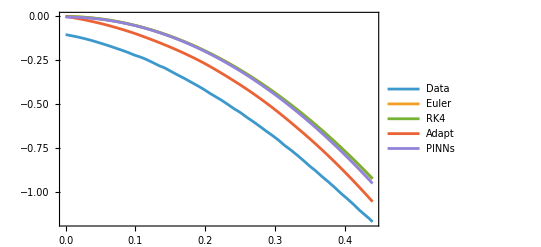

```mathematica
Plot[{dataInterpolated[t],eulerInterpolated[t],rk4Interpolated[t],adaptInterpolated[t] ,pinnInterpolated[t] },{t,0,.44}, Frame->True, PlotLegends->{"Data", "Euler", "RK4", "Adapt", "PINNs"}]
```

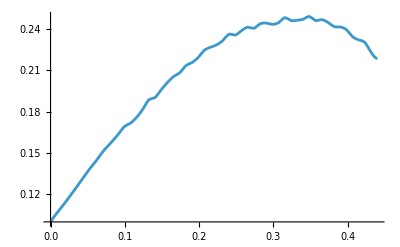

```mathematica
Plot[Abs[dataInterpolated[t]-pinnInterpolated[t]],{t,0,.44}]
```

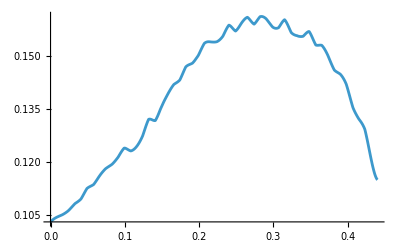

```mathematica
Plot[Abs[dataInterpolated[t]-adaptInterpolated[t]],{t,0,.44}]
```

```mathematica
Sqrt[1/(0.44-0.0)×NIntegrate[(dataInterpolated[t]-adaptInterpolated[t])^2,{t,0,0.44}]]
```

0.139968

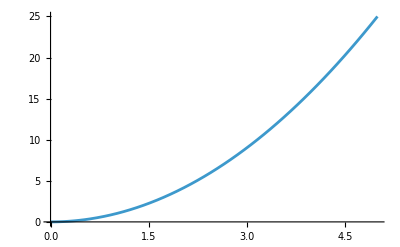

```mathematica
f[x_]:=x^2;
error[x_]:=10.1*x;
Plot[Around[f[x],error[x]],{x,0,5}]
```

```mathematica
dataInterpolatedWithErorrs = Table[{i,Around[adaptInterpolated[i],0.14]},{i,0,0.44,0.01}];
```

```mathematica
dataFull = Table[{i,dataInterpolated[i]},{i,0,0.44,0.01}];
```

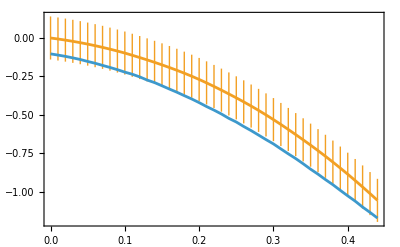

```mathematica
ListLinePlot[{dataFull,dataInterpolatedWithErorrs}, Frame->True]
```